{-2 Vy[t]-X[t]+(0.5 (-0.5+X[t]))/(((0.5-X[t])^2+Y[t]^2)^(3/2))+(0.5 (0.5+X[t]))/(((0.5+X[t])^2+Y[t]^2)^(3/2))+Vx'[t]==0,2 Vx[t]-Y[t]+(0.5 Y[t])/(((0.5-X[t])^2+Y[t]^2)^(3/2))+(0.5 Y[t])/(((0.5+X[t])^2+Y[t]^2)^(3/2))+Vy'[t]==0,-Vx[t]+X'[t]==0,-Vy[t]+Y'[t]==0,X[0]==0.044,Vx[0]==0.,Y[0]==0.,Vy[0]==0.}

NDSolve::precw: The precision of the differential equation ({-2 Vy[t] - X[t] + 0.5` (-0.5` + X[t])/(Power[« 2 »] + Power[« 2 »])^3/2 + 0.5` (0.5`  + X[t])/(Power[« 2 »] + Power[« 2 »])^3/2 + SuperscriptBox[« 3 »{}) is less than WorkingPrecision (32.).

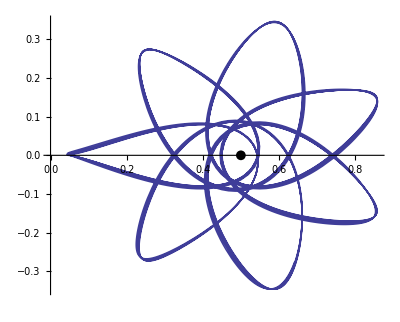

motionADAMS.jpg

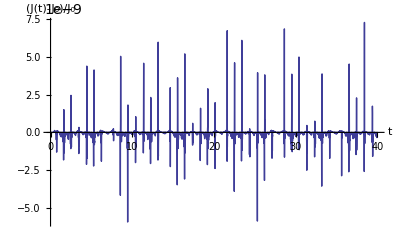

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:IntegrMethod^(***)
* Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Using the Adams Method to calculate the orbit in the restricted three body problem and check the error of the method with the variation in time of the Jacobi Constant. Because is an integral of motion this value must be always equal to itself. 
   * Invocation: DifferentialEquations
*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Clear[Omega,r1,r2,X,Y,mu,Vx,Vy]

tin=0.;
tfin=40;

Omega=(1/2)((1-mu)r1^2+mu r2^2)+mu/r2+(1-mu)/r1;

r1=((X[t]-mu)^2+Y[t]^2)^(1/2);
r2=((X[t]+1-mu)^2+Y[t]^2)^(1/2);

VxEquation=Simplify[
	D[Vx[t],t]-2Vy[t]-D[Omega,X[t]]];
VyEquation=Simplify[
	D[Vy[t],t]+2Vx[t]-D[Omega,Y[t]]];
xEquation=D[X[t],t]-Vx[t];
yEquation=D[Y[t],t]-Vy[t];

Clear[X,Y,Vx,Vy]

mu=.5;

InitialConditions={X[0]==0.044,Vx[0]==0.,Y[0]==0.,Vy[0]==0.};

EquationList=Join[
    {VxEquation==0},{VyEquation==0},
	{xEquation==0},{yEquation==0},
	InitialConditions]
Orbit=NDSolve[EquationList,{X[t],Y[t],Vx[t],Vy[t]},{t,tin,tfin},
	      Method -> "Adams", WorkingPrecision -> 32, PrecisionGoal->30, MaxSteps->50000];

X[t_]=First[X[t]/.Orbit];
Y[t_]=First[Y[t]/.Orbit];
Vx[t_]=First[Vx[t]/.Orbit];
Vy[t_]=First[Vy[t]/.Orbit];

r=ParametricPlot[{X[t],Y[t]},{t,tin,tfin},
	AspectRatio->Automatic,PlotPoints->100,
Epilog->{AbsolutePointSize[7],
Point[{mu-1,0}],Point[{mu,0}]}]
Export["motionADAMS.jpg",r]
C0=(2 Omega-Vx[t]^2-Vy[t]^2)/.t->0;
deltaC=(2 Omega-Vx[t]^2-Vy[t]^2-C0)/C0;
k=Plot[Evaluate[deltaC],{t,tin,tfin},
	PlotRange->All,AxesLabel->{"t","(J(t)-\!\(\*SubscriptBox[\(J\), \(0\)]\))/\!\(\*SubscriptBox[\(J\), \(0\)]\)"}]
(* Export["intgrADAMS.jpg",k] *)
```